```mathematica
toFunc[func_, var_] := Evaluate[Unevaluated[func] /. {var -> #}] & ;

g0Poisson[z_, c_] := Exp[c(z -1)] ;
g0ScaleFree[z_, α_] := PolyLog[α, z]/Zeta[α] ;
```

```mathematica
Manipulate[Plot[{u, 1  - (1 - g0Poisson[u, c1])(1 - g0Poisson[u, c1])}, {u, 0, 1},
PlotRange->{{0, 1}, {0, 1}},
AspectRatio-> 1], 
{c1, 2, 3}]
```

```mathematica
g0 = g0ScaleFree ;
dg0 = Derivative[1, 0][g0] ;
g1 = dg0[#1, #2]/dg0[1, #2]& ;
u[p_] := FixedPoint[g1[#, p]&, 10.^-8, SameTest -> (Abs[#1 - #2] < 10.^-8 &)] ;
S[p_] := 1 - g0[u[p], p] ;
ListPlot[ParallelTable[{p, S[p]}, {p, 2.1, 4, 0.1}], Joined -> True]
```

$Aborted

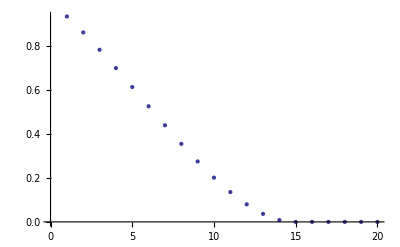

```mathematica
Plot[S[p], {p, 2.1, 4}]
```

```mathematica
FixedPoint[g1[#, 3.1] &, 10.^-7, SameTest -> (#1 - #2 < 0.0001 &)]
g1[z, c]
```

0.640937

PolyLog[-1+c,z]/(z PolyLog[-1+c,1])

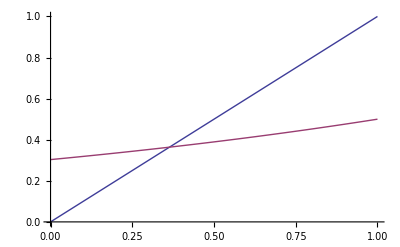

```mathematica
Plot[{z, g1[z, 0.5]}, {z, 0, 1}]
```

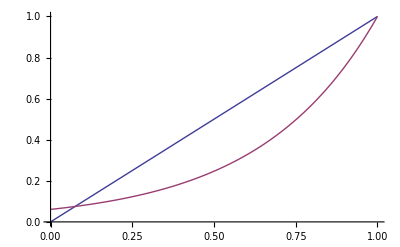

```mathematica
Plot[{u, g1Poisson[u,2.8]}, {u, 0, 1}]
```

```mathematica
NestList[g1ScaleFree[#, 2.8] &, 10.^-7, 50]
```

{1.×10^-7,0.531285,0.643528,0.681325,0.69622,0.702469,0.705162,0.706336,0.70685,0.707076,0.707175,0.707218,0.707237,0.707246,0.70725,0.707251,0.707252,0.707252,0.707252,0.707252,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253,0.707253}

```mathematica
FixedPoint[g1Poisson[#, 1.5] &, 10.^-7]
```

0.417188

```mathematica
g[x_, y_] := y x^2 + y^3 ;
Derivative[1, 1][g]
```

2 #1&

```mathematica
g1
```

ⅇ^((-1+#1) #2) #2&

```mathematica
test = g1/3
```

1/3 (ⅇ^((-1+#1) #2) #2&)

```mathematica
test[z, c]
```

(1/3 (ⅇ^((-1+#1) #2) #2&))[z,c]